# Figure 2B and Supplementary Table S4C

```mathematica
Clear["Global`*"]
```

```mathematica
data=Import[NotebookDirectory[]<>"Volume Changes And Tumor Types.csv","CSV"];
```

```mathematica
data⟦1;;10⟧//TableForm
```

Patient # | Volume Change | Tumor Type
1 | 68 | Gastroesophageal
2 | 56 | Ampulla of Vater
3 | 48 | Osteosarcoma
4 | 47 | Gastroesophageal
5 | 36 | Colorectal
6 | 36 | Endometrial
7 | 23 | Endometrial
8 | 17 | Colorectal
9 | 17 | Small intestine

## analysis of all tumor types

```mathematica
AllVolumeChangeMeasurements=Select[data⟦2;;,2⟧,#≠"NA"&];
```

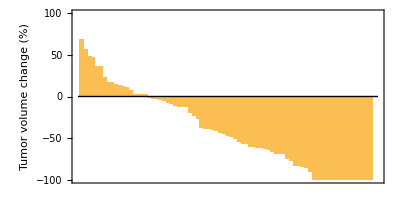

```mathematica
BarChart[Reverse[Sort[AllVolumeChangeMeasurements]],BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Black,Thickness[Medium]],PlotRange->{-100,100},PlotRangePadding->None,Frame->{{True,False},{False,False}},Axes->{True,False},AxesOrigin->{0,0},FrameLabel->{,"Tumor volume change (%)"},ImageSize->{{1000},{200}},AspectRatio->1/2]
```

```mathematica
Length[Select[AllVolumeChangeMeasurements,#<-30&]]/Length[AllVolumeChangeMeasurements]//N
```

0.589744

```mathematica
RandomSamplePlot[samplesize_]:=BarChart[Reverse[Sort[RandomSample[Reverse[Sort[AllVolumeChangeMeasurements]],samplesize]]],BaseStyle->{FontFamily->"Arial",FontSize->12},FrameStyle->Directive[Black,Thickness[Medium]],PlotRange->{-100,100},PlotRangePadding->None,Frame->{{True,False},{False,False}},Axes->{True,False},AxesOrigin->{0,0},(*FrameLabel->{,"Tumor volume change (%)"},*)AspectRatio->4,ImageSize->{{1000},{200}},ChartStyle->EdgeForm[None]]
```

```mathematica
VolumeChangeMeasurementsAndTumorType=Select[data⟦2;;,{3,2}⟧,#⟦2⟧≠"NA"&];
```

```mathematica
TumorTypes=Sort[Tally[VolumeChangeMeasurementsAndTumorType⟦All,1⟧],#1⟦2⟧>#2⟦2⟧&];
TumorTypes//TableForm
```

Colorectal | 37
Endometrial | 14
Pancreas | 6
Small intestine | 5
Gastroesophageal | 5
Cholangiocarcinoma | 4
Ampulla of Vater | 3
Prostate | 1
Neuroendocrine | 1
Unknown Primary | 1
Osteosarcoma | 1

```mathematica
PatientsPerTumorType=TumorTypes⟦All,2⟧
```

{37,14,6,5,5,4,3,1,1,1,1}

```mathematica
MeanResponsePerTumorType=Table[{TumorTypes⟦i,1⟧,Mean[Select[VolumeChangeMeasurementsAndTumorType,#⟦1⟧==TumorTypes⟦i,1⟧&]⟦All,2⟧]//N},{i,1,Length[TumorTypes]}];
MeanResponsePerTumorType//TableForm
MedianResponsePerTumorType=Table[{TumorTypes⟦i,1⟧,Median[Select[VolumeChangeMeasurementsAndTumorType,#⟦1⟧==TumorTypes⟦i,1⟧&]⟦All,2⟧]//N},{i,1,Length[TumorTypes]}];
MedianResponsePerTumorType//TableForm
```

Colorectal | -37.9189
Endometrial | -41.7857
Pancreas | -58.1667
Small intestine | -55.8
Gastroesophageal | -37.
Cholangiocarcinoma | -34.75
Ampulla of Vater | -15.3333
Prostate | -100.
Neuroendocrine | -69.
Unknown Primary | -37.
Osteosarcoma | 48.

Colorectal | -43.
Endometrial | -52.5
Pancreas | -48.5
Small intestine | -61.
Gastroesophageal | -100.
Cholangiocarcinoma | -21.
Ampulla of Vater | -2.
Prostate | -100.
Neuroendocrine | -69.
Unknown Primary | -37.
Osteosarcoma | 48.

#### simulating null hypothesis

```mathematica
samplesize=10^7;
ManySamplesOfTrialMatchedSize=Table[
{TumorTypes⟦i,1⟧,Table[Mean[RandomSample[AllVolumeChangeMeasurements,TumorTypes⟦i,2⟧]],{samplesize}]}
,{i,1,Length[TumorTypes]}];
```

### Probability of larger benefit

```mathematica
PValuesByTumorType=Table[{TumorTypes⟦i,1⟧,Length[Select[ManySamplesOfTrialMatchedSize⟦i,2⟧,#<MeanResponsePerTumorType⟦i,2⟧&]]/samplesize//N},{i,1,11}]⟦{1,2,3,4,5,6,7}⟧
```

{{Colorectal,0.663889},{Endometrial,0.451168},{Pancreas,0.169064},{Small intestine,0.229471},{Gastroesophageal,0.569259},{Cholangiocarcinoma,0.599857},{Ampulla of Vater,0.81891}}

```mathematica
SortedPValues=Join[{Range[7]},Sort[PValuesByTumorType,#1⟦2⟧<#2⟦2⟧&]ᵀ]ᵀ;
SortedPValues//TableForm
```

1 | Pancreas | 0.169064
2 | Small intestine | 0.229471
3 | Endometrial | 0.451168
4 | Gastroesophageal | 0.569259
5 | Cholangiocarcinoma | 0.599857
6 | Colorectal | 0.663889
7 | Ampulla of Vater | 0.81891

```mathematica
SortedPValuesForTissueTypes=SortedPValues
```

{{1,Pancreas,0.169064},{2,Small intestine,0.229471},{3,Endometrial,0.451168},{4,Gastroesophageal,0.569259},{5,Cholangiocarcinoma,0.599857},{6,Colorectal,0.663889},{7,Ampulla of Vater,0.81891}}

#### two - sided test

```mathematica
Table[{SortedPValuesForTissueTypes⟦i,1⟧,SortedPValuesForTissueTypes⟦i,2⟧,SortedPValuesForTissueTypes⟦i,3⟧,(* benjamini-hochberg critical value: (i/m)*Q *)((i)/Length[SortedPValuesForTissueTypes]*(* Q = 0.25 *)0.25/2//N)},{i,1,Length[SortedPValuesForTissueTypes]}]//TableForm
Length[SortedPValuesForTissueTypes]
```

1 | Pancreas | 0.169064 | 0.0178571
2 | Small intestine | 0.229471 | 0.0357143
3 | Endometrial | 0.451168 | 0.0535714
4 | Gastroesophageal | 0.569259 | 0.0714286
5 | Cholangiocarcinoma | 0.599857 | 0.0892857
6 | Colorectal | 0.663889 | 0.107143
7 | Ampulla of Vater | 0.81891 | 0.125

7

### Probability of smaller benefit

```mathematica
PValuesByTumorType=Table[{TumorTypes⟦i,1⟧,Length[Select[ManySamplesOfTrialMatchedSize⟦i,2⟧,#>MeanResponsePerTumorType⟦i,2⟧&]]/samplesize//N},{i,1,11}]⟦{1,2,3,4,5,6,7}⟧
```

{{Colorectal,0.334358},{Endometrial,0.54637},{Pancreas,0.828517},{Small intestine,0.767575},{Gastroesophageal,0.427},{Cholangiocarcinoma,0.395894},{Ampulla of Vater,0.177999}}

```mathematica
SortedPValues=Join[{Range[7]},Sort[PValuesByTumorType,#1⟦2⟧<#2⟦2⟧&]ᵀ]ᵀ;
SortedPValues//TableForm
```

1 | Ampulla of Vater | 0.177999
2 | Colorectal | 0.334358
3 | Cholangiocarcinoma | 0.395894
4 | Gastroesophageal | 0.427
5 | Endometrial | 0.54637
6 | Small intestine | 0.767575
7 | Pancreas | 0.828517

```mathematica
SortedPValuesForTissueTypes=SortedPValues
```

{{1,Ampulla of Vater,0.177999},{2,Colorectal,0.334358},{3,Cholangiocarcinoma,0.395894},{4,Gastroesophageal,0.427},{5,Endometrial,0.54637},{6,Small intestine,0.767575},{7,Pancreas,0.828517}}

#### two - sided test

```mathematica
Table[{SortedPValuesForTissueTypes⟦i,1⟧,SortedPValuesForTissueTypes⟦i,2⟧,SortedPValuesForTissueTypes⟦i,3⟧,(* benjamini-hochberg critical value: (i/m)*Q *)((i)/Length[SortedPValuesForTissueTypes]*(* Q = 0.25 *)0.25/2//N)},{i,1,Length[SortedPValuesForTissueTypes]}]//TableForm
Length[SortedPValuesForTissueTypes]
```

1 | Ampulla of Vater | 0.177999 | 0.0178571
2 | Colorectal | 0.334358 | 0.0357143
3 | Cholangiocarcinoma | 0.395894 | 0.0535714
4 | Gastroesophageal | 0.427 | 0.0714286
5 | Endometrial | 0.54637 | 0.0892857
6 | Small intestine | 0.767575 | 0.107143
7 | Pancreas | 0.828517 | 0.125

7

### Plotting null distributions per tumor type

```mathematica
ph (* plot height *)=0.16;
(* New version - labels of tumor type and population on the side *)
HistogramOfMeanResponseWithinATumorType[i_]:=Module[{},

myplot=Histogram[ManySamplesOfTrialMatchedSize⟦i,2⟧,{-100,50,2.5},"Probability",(*PlotLabel->Style[ManySamplesOfTrialMatchedSize⟦i,1⟧,Black,FontSize->11,FontFamily->"Arial"],*)PlotRange->{{-100,50},{0,All}},PlotRangePadding->None,Frame->{{True,False},{True,False}},FrameStyle->{Dashing[{0,1}],Directive[Black,Thickness[Medium]]},Epilog->{Red,AbsoluteThickness[2],Line[{{MeanResponsePerTumorType⟦i,2⟧,0},{MeanResponsePerTumorType⟦i,2⟧,ph}}]},ChartStyle->Directive[EdgeForm[None],Lighter[ColorData[3,6],0.5]],FrameTicks->{Join[Table[{j,j,{0,0.03}},{j,-100,100,50}](*,Table[{j,,{0,0.015}},{j,-100,100,10}]*)],None(*Join[Table[{j,100*j,{0,0.02}},{j,0,10/100,2/100}],Table[{j,,{0,0.01}},{j,0,10/100,2/100}]]*)},BaseStyle->{FontFamily->"Arial",FontSize->10},AspectRatio->0.2,ImagePadding->{{200,20},{40,5}},FrameLabel->{None,Rotate[Style[ManySamplesOfTrialMatchedSize⟦i,1⟧<>"   "<>ToString[Round[PatientsPerTumorType⟦i⟧]]<>" ",Black,FontSize->11,FontFamily->"Arial"],-π/2]},ImageSize->{{350},{100}}];

Export[NotebookDirectory[]<>"AverageVolumeByTumor - "<>ManySamplesOfTrialMatchedSize⟦i,1⟧<>".PDF", myplot,"PDF"];

]
```

```mathematica
Do[
HistogramOfMeanResponseWithinATumorType[i]
,{i,1,7}];
```